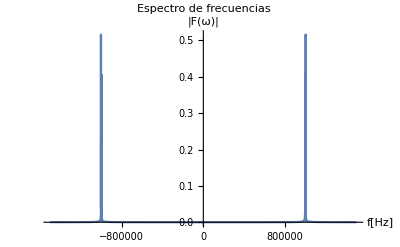

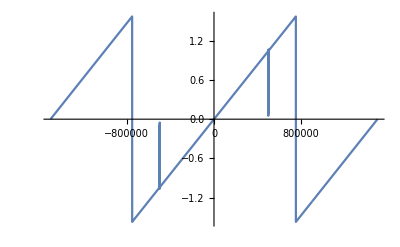

```mathematica
Clear["Global`*"]
(*Datos de muestreo*)
fs=3*10^6; (*<- Frecuencia de muestreo*)
ps = 1/fs; (*<- Periodo de muestreo*)
L=10000; (*<- Numero de muestras*)

(*vector tiempo*)
t=ps*Range[0,L-1];
(*vector frecuencia*)
f=(fs/2)*Range[-1+2/L,1,2/L];
(*Función a Muestrear*)
mensaje= 2*Cos[2*2000π*t] + Cos[2*1000π*t];
portadora = Cos[2*π*10^6*t];
modulada = mensaje*portadora;
(*Transformada de F. de la funcion muestreada*)
fouriermensaje = Fourier[modulada,FourierParameters->{1, -1}]/L;
(*Espectro de frecuencias*)
ListLinePlot[Transpose[{f,RotateRight[Abs[fouriermensaje],Ceiling[L/2]-1]}],
PlotRange->All,
AxesLabel->{"f[Hz]","|F(ω)|"},
PlotLabel->"Espectro de frecuencias"]
(*desfase*)
desfase = Table[ArcTan[Im[fouriermensaje [[i]]]/Re[fouriermensaje [[i]]]],{i,1,L}];
ListLinePlot[Transpose[{f,desfase}]]
```

s/(-10+s)^2TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#SDPLink`s11SDPLink`s-101FalseFalseFalseAutomaticNoneAutomatic

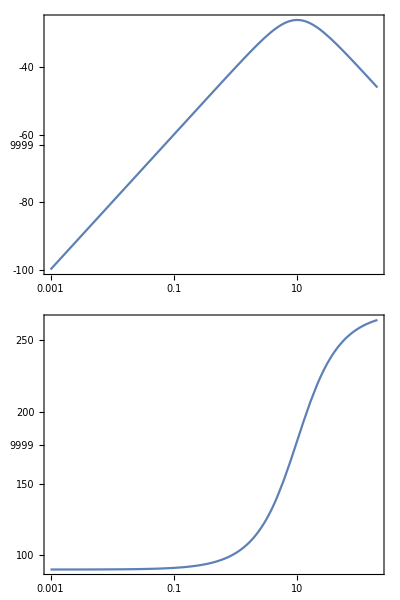

```mathematica
a=TransferFunctionModel[H = (s)/(s-10)^2,s]
BodePlot[a]
```